```mathematica
Exit[];
```

```mathematica
PrependTo[$Path,"D:\\Users\\Johannes\\Promotion\\SVN Rep\\Mathematica\\Packages"];<<JoFin`
```

```mathematica
f[x_]:=Log[If[x[[1]]==x[[2]],10^(-15),Abs[x[[1]]-x[[2]]]/(Abs[x[[1]]]+Abs[x[[2]]])]]/Log[10]
```

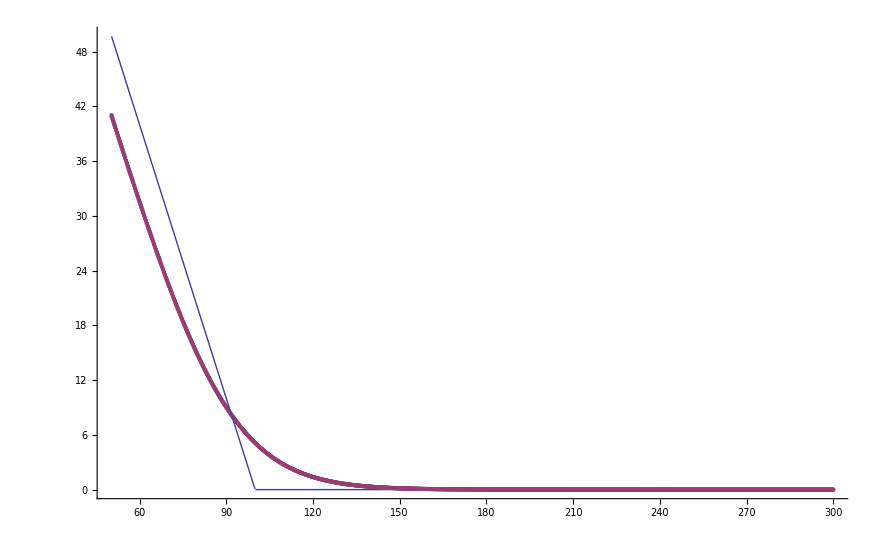

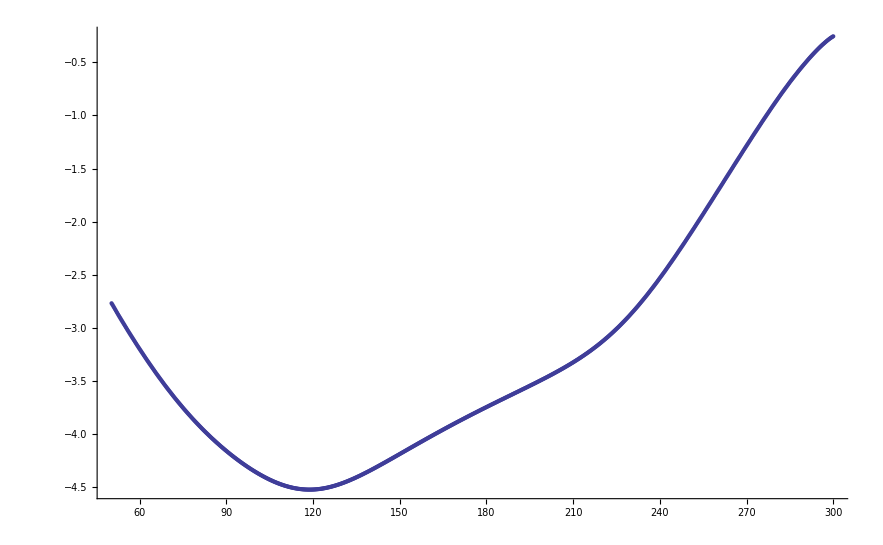

-∞

```mathematica
σ=0.2;ρ=0.3;n=2;r=0.05;T=2;k=100;
{σ,d}=IsometricGeometricAverageParameters[σ,0,ρ,n];
a=Import["D:\\Users\\Johannes\\Promotion\\SVN Rep\\Programmierung\\Tridiagonal Solver Tests\\output\\cut.txt","Table"];
nn=Length[a];
a=a[[;;nn]];
b={#[[1]],BlackScholesPut[#[[1]],k,T,r,σ,d]}&/@a;
(*b=c;*)
Show[ListPlot[{a,b},PlotRange->All],Plot[Max[k-x ,0],{x,Min[a[[;;,1]]],Max[a[[;;,1]]]},PlotRange->All ]]
(*ListPlot[Transpose[{a[[;;,1]],f/@Transpose[{a[[;;,2]],c[[;;,2]]}]}]]
Max[Select[Transpose[{a[[;;,1]],f/@Transpose[{a[[;;,2]],c[[;;,2]]}]}],90≤ #[[1]]≤110&][[;;,2]]]*)
ListPlot[Transpose[{a[[;;,1]],f/@Transpose[{a[[;;,2]],b[[;;,2]]}]}]]
Max[Select[Transpose[{a[[;;,1]],f/@Transpose[{a[[;;,2]],b[[;;,2]]}]}],650≤ #[[1]]≤670&][[;;,2]]]
```